# Wes’s Haversin Puzzle

## Functions and Unit Tests

http://en.wikipedia.org/wiki/Haversine_formula 
http://en.wikipedia.org/wiki/Great-circle_distance 
http://geospatialmethods.org/spheres/GCIntersect.html
http://www.bing.com/community/site_blogs/b/maps/default.aspx
http://www.bing.com/community/site_blogs/b/maps/archive/2010/05/19/new-bing-map-apps-gas-prices-distance-calculator-and-parking-finder.aspx
http://www.planetmarshall.co.uk/2010/06/drawing-geodesic-curves-using-the-bing-maps-silverlight-control/

```mathematica
deg = π/180;
```

```mathematica
haversin[θ_]:=Sin[θ/2]^2
```

```mathematica
haversinDistance[R_,{lat1_,lon1_},{lat2_,lon2_}]:=
With[{h=haversin[(lat2-lat1)]+Cos[lat1 ]Cos[lat2]*
haversin[(lon2-lon1)]},
2R ArcSin[Sqrt[h]]]
```

A second of arc should be about 100 feet (30 m)

```mathematica
haversinDistance[6356.14 * 1000meter,{0,0},{deg/3600,0}]
```

30.8154 meter

```mathematica
haversinDistance[ll1_List,ll2_List]:=haversinDistance[6356.14 * 1000meter,ll1,ll2]
```

A thousands of a degree (one in the last place in the plots above) is about 364 feet:

```mathematica
haversinDistance[{0,0},{0.001 deg,0}]
```

110.936 meter

```mathematica
haversinDistance[{0,0},{0.001 deg,0}]*1250 feet/(381 meter)
```

363.962 feet

How much is a millionth of a degree (at the equator)?

```mathematica
haversinDistance[{0,0},{0.000001 deg,0}]
```

0.110936 meter

about 11.0936 centimeters, or about

```mathematica
11.0936 cm/(2.54 cm / inch)
```

4.36756 inch

For more accuracy, try this: http://en.wikipedia.org/wiki/Vincenty%27s_formulae

## The Puzzle

quote:

For some definition of fun and assuming that the earth is a perfect sphere with radius R, we would like to compute what segment of an arc between two points on the surface of a spherical cap described by a point and a distance. 
Here are the details. We have a latitude and longitude of a hotspot, C, which is the center of a boundary. The boundary contains all points whose distance to the center, C, is less than or equal to d. 
Now given two more points in latitude and longitude, A and B we want to compute a distance on the surface of the sphere between A and B which doesn’t overlap with the boundary. 
Lunch on me for a correct answer, an explanation, and a derivation of the haversine formula. 
- Wes & Bart

end quote

```mathematica
ptA={latA,lonA};
ptB={latB,lonB};
```

Must assume that A and B are both on the same side of the boundary, lest the geodesic connecting them cross the boundary. 
If they’re both on the inside of the boundary, then the distance is simply the haversin formula

```mathematica
haversinDistance[R,ptA,ptB]
```

2 R sin^-1(√(cos(latA) cos(latB) sin^2((lonB-lonA)/2)+sin^2((latB-latA)/2)))

If they’re both on the outside, then the geodesic between them may be required to “ride” the boundary for a while . . .

## WLOG

WLOG (without loss of generality), imagine the unit sphere and that point C is the North Pole, with coordinates {0, 0, 1}.

```mathematica
latLonToXYZ[R_,{lat_,lon_}]:=
{R Cos[lat]Cos[lon],
R Cos[lat]Sin[lon],
R Sin[lat]}
```

The set of points of constant radius 1 that go through A and B define the great circle connecting them:

The equation of a Great Circle in the form of latitude as a function of longitude, easy for parametric rendering

```mathematica
latC[lonC_,{lat1_,lon1_},{lat2_,lon2_}]:=
With[{
y=Sin[lat1]Cos[lat2]Sin[lon2-lonC]-Sin[lat2]Cos[lat1]Sin[lon1-lonC],
x=Cos[lat1]Cos[lat2]Sin[lon2-lon1]},
ArcTan[x,y]]
```

The circumpolar arc is simply the set of points of constant latitude as longitude varies from 0 through 360.

```mathematica
With[{
pA={35,-120}deg,
pB={18,40}deg,
Radius=1},
With[{
A=latLonToXYZ[1,pA],
B=latLonToXYZ[1,pB],
Center={0,0,0},
Pole={0,0,1}},
Show[
Graphics3D[{Opacity[0.6250],Sphere[Center],
Text["A",A],
Text["B",B],
Text["C",Pole]
},
AspectRatio->1],
(* The circumpolar boundary *)
ParametricPlot3D[
latLonToXYZ[Radius,{65,lon}deg],
{lon,0,360},
AspectRatio->1],
(* The Great-Circle semi-arc *)
ParametricPlot3D[
latLonToXYZ[Radius,{latC[lon,pA,pB],lon}],
{lon,pA⟦2⟧,pB⟦2⟧}]
]]]
```

-Graphics3D-

## Finding the Intersection Points

The following is the lat as a function of lon for the great circle:

```mathematica
latC[LON,ptA,ptB]
```

tan^-1(-cos(latA) cos(latB) sin(lonA-lonB),cos(latA) sin(latB) sin(LON-lonA)-sin(latA) cos(latB) sin(LON-lonB))

Solve for the longitude for a given LAT to find the intersection points:

(Don’t run this -- never finishes)

```mathematica
Solve[LAT==latC[LON,ptA,ptB],
LON,
Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[LAT==tan^-1(-cos(latA) cos(latB) sin(lonA-lonB),cos(latA) sin(latB) sin(LON-lonA)-sin(latA) cos(latB) sin(LON-lonB)),LON,ℝ]

```mathematica
LAT==latC[LON,ptA,ptB]
```

LAT==tan^-1(-cos(latA) cos(latB) sin(lonA-lonB),cos(latA) sin(latB) sin(LON-lonA)-sin(latA) cos(latB) sin(LON-lonB))

Try a numerical solution

```mathematica
numericalRule={
LAT->65.0 deg,
latA->35.0deg,
lonA->-120.0deg,
latB->18.0deg,
lonB->40.0deg}
```

{LAT→1.13446,latA→0.610865,lonA→-2.0944,latB→0.314159,lonB→0.698132}

```mathematica
numExact={
LAT->65deg,
latA->35deg,
lonA->-120deg,
latB->18deg,
lonB->40deg}
```

{LAT→(13 π)/36,latA→(7 π)/36,lonA→-(2 π)/3,latB→π/10,lonB→(2 π)/9}

```mathematica
LAT==latC[LON,ptA,ptB]/.numExact
```

(13 π)/36==tan^-1(√(5/8+(√5)/8) sin(π/9) cos((7 π)/36),1/4 (√5-1) cos((7 π)/36) cos(LON+π/6)-√(5/8+(√5)/8) sin((7 π)/36) sin(LON-(2 π)/9))

This one takes too long ... I didn’t let it finish

```mathematica
Solve[LAT==latC[LON,ptA,ptB]/.numExact,
LON,
Reals]
(* doesn't finish in 5 days with: //FullSimplify *)
```

{{LON→«1»},{LON→ConditionalExpression[2 π c_1+2 tan^-1((-√2+«28»+(4 («1»)^(«1») «1» √(-(2 «1»)/(«1»)))/(-1+(-1)^(5/18)))/((1+-1^(1/18)) (-(-1)^(11/18) √6+«49»+(2 «2» √(5+«1»))/(-1+(«1»)^(«1»))))),(c_1∈ℤ∧(«1»)/(«1»)<«1»<√((«1»)/(«1»)))∨«1»]}}

This was as close as we could get using MMA’s tools. This tells us that, in a C# implementation, we must (A) consider the principal branches of the trig functions (B) probably resort to a custom tailored Newton’s method. But I’m convinced we can do it :)

```mathematica
NSolve[
LAT==latC[LON,ptA,ptB]/.numericalRule,
LON,
Reals]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{LON→ConditionalExpression[1. (6.28319 c_1-1.52233),c_1∈ℤ]},{LON→ConditionalExpression[1. (6.28319 c_1-0.00285341),c_1∈ℤ]}}

```mathematica
NSolve[
LAT==latC[LON,ptA,ptB]/.numExact,
LON,
Reals]//Chop
```

Less::nord: Invalid comparison with TraditionalForm`-2.13869 + 9.99201×10^-16\ ⅈ attempted.

Less::nord: Invalid comparison with TraditionalForm`2.14451  - 1.11022×10^-16\ ⅈ
 attempted.

Less::nord: Invalid comparison with TraditionalForm`-2.13869 + 9.99201×10^-16\ ⅈ attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

{{LON→ConditionalExpression[1. (6.28319 c_1-0.00285341),c_1∈ℤ]},{LON→ConditionalExpression[1. (6.28319 c_1-1.52233),c_1∈ℤ]}}

See if they’re plausible, by copying the solution by hand into the following and plotting

```mathematica
With[{
lat=65deg,
pA={35,-120}deg,
pB={18,40}deg,
Radius=1},
With[{
A=latLonToXYZ[1,pA],
B=latLonToXYZ[1,pB],
Center={0,0,0},
Pole={0,0,1}},
Show[
Graphics3D[{Opacity[0.6250],Sphere[Center],
Text["A",A],
Text["B",B],
Text["C",Pole],
PointSize[Large],
Point[latLonToXYZ[Radius,{lat,(6.28319-1.52233)}]],
Point[latLonToXYZ[Radius,
{lat,(6.28318-0.00285340)}]]
},
AspectRatio->1],
(* The circumpolar boundary *)
ParametricPlot3D[
latLonToXYZ[Radius,{lat,lon}],
{lon,0,360deg},
AspectRatio->1],
(* The Great-Circle semi-arc *)
ParametricPlot3D[
latLonToXYZ[Radius,{latC[lon,pA,pB],lon}],
{lon,pA⟦2⟧,pB⟦2⟧}]
]]]
```

-Graphics3D-

Pop the cork and declare victory

## Failed Junk

## AMissing Simplification Formulas

Hard to believe, but Mathematica apparently doesn’t know the following:

```mathematica
Cos[ArcTan[x,y]]/.{Cos[ArcTan[x_,y_]]->x/(√(x^2+y^2))}
```

x/(√(x^2+y^2))

```mathematica
Plot3D[Cos[ArcTan[x,y]],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[x/(√(x^2+y^2)),{x,-2,2},{y,-2,2}]
```

-Graphics3D-

Break it up

```mathematica
expr1=latLonToXYZ[1,{LAT,LON}]
```

{cos(LAT) cos(LON),cos(LAT) sin(LON),sin(LAT)}

```mathematica
(expr2=latLonToXYZ[1,{latC[LON,ptA,ptB],LON}])//FullSimplify
```

{cos(LON) cos(tan^-1(-cos(latA) cos(latB) sin(lonA-lonB),cos(latA) sin(latB) sin(LON-lonA)-sin(latA) cos(latB) sin(LON-lonB))),sin(LON) cos(tan^-1(-cos(latA) cos(latB) sin(lonA-lonB),cos(latA) sin(latB) sin(LON-lonA)-sin(latA) cos(latB) sin(LON-lonB))),sin(tan^-1(-cos(latA) cos(latB) sin(lonA-lonB),cos(latA) sin(latB) sin(LON-lonA)-sin(latA) cos(latB) sin(LON-lonB)))}

```mathematica
(expr3=(expr2/.{
Cos[ArcTan[x_,y_]]->x/(√(x^2+y^2)),
Sin[ArcTan[x_,y_]]->y/(√(x^2+y^2))}))//FullSimplify
```

{-(cos(latA) cos(latB) cos(LON) sin(lonA-lonB))/(√((cos(latA) sin(latB) sin(LON-lonA)-sin(latA) cos(latB) sin(LON-lonB))^2+cos^2(latA) cos^2(latB) sin^2(lonA-lonB))),-(cos(latA) cos(latB) sin(LON) sin(lonA-lonB))/(√((cos(latA) sin(latB) sin(LON-lonA)-sin(latA) cos(latB) sin(LON-lonB))^2+cos^2(latA) cos^2(latB) sin^2(lonA-lonB))),(cos(latA) sin(latB) sin(LON-lonA)-sin(latA) cos(latB) sin(LON-lonB))/(√((cos(latA) sin(latB) sin(LON-lonA)-sin(latA) cos(latB) sin(LON-lonB))^2+cos^2(latA) cos^2(latB) sin^2(lonA-lonB)))}

Let’s try a numerical solution

```mathematica
numericalRule={
LAT->65.0 deg,
latA->35.0deg,
lonA->-120.0deg,
latB->18.0deg,
lonB->40.0deg}
```

{LAT→1.13446,latA→0.610865,lonA→-2.0944,latB→0.314159,lonB→0.698132}

```mathematica
expr1/.numericalRule
```

{0.422618 cos(LON),0.422618 sin(LON),0.906308}

```mathematica
expr1==expr3/.numericalRule
```

{0.422618 cos(LON),0.422618 sin(LON),0.906308}=={(0.266454 cos(LON))/(√((0.545504 sin(0.698132-LON)+0.253132 sin(LON+2.0944))^2+0.0709978)),(0.266454 sin(LON))/(√((0.545504 sin(0.698132-LON)+0.253132 sin(LON+2.0944))^2+0.0709978)),(0.545504 sin(0.698132-LON)+0.253132 sin(LON+2.0944))/(√((0.545504 sin(0.698132-LON)+0.253132 sin(LON+2.0944))^2+0.0709978))}

Numerical Solve not able to find an answer :(

```mathematica
NSolve[expr1==expr3/.numericalRule,LON]
```

NSolve::ifun: Inverse functions are being used by TraditionalForm`NSolve, so some solutions may not be found; use Reduce for complete solution information.

{}

Hopeless for regular Solve

```mathematica
Solve[expr1==expr3/.numericalRule,LON]
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

{}

Try by hand

```mathematica
expr1
```

{cos(LAT) cos(LON),cos(LAT) sin(LON),sin(LAT)}

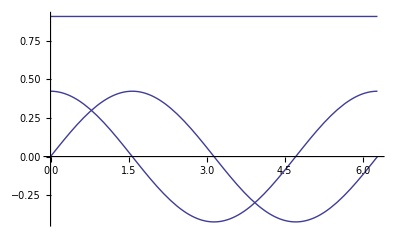

```mathematica
Plot[expr1/.numericalRule,{LON,0,360deg}]
```

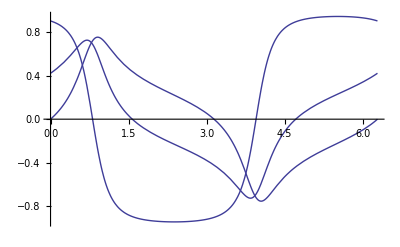

```mathematica
Plot[expr3/.numericalRule,{LON,0,360deg}]
```

Find intersections by component: